```mathematica
SetDirectory["/Users/JMB/Documents/code/bem3d_ves_tube/blood95/conf90/v1eb05/D"];fnumber=16300;SetDirectory["/Users/JMB/Documents/code/bem3d_ves_tube/blood95/conf90/v1eb1/D"];fnumber=14900;
SetDirectory["/Users/JMB/Documents/code/bem3d_ves_tube/blood95/conf90/v1eb2/D"];fnumber=12800;
SetDirectory["/Users/JMB/Documents/code/bem3d_ves_tube/blood95/conf90/v1eb4/D"];fnumber=9200;
SetDirectory["/Users/JMB/Documents/code/bem3d_ves_tube/blood95/conf90/v1eb10/D"];fnumber=6200;
SetDirectory["/Users/JMB/Documents/code/bem3d_ves_tube/blood95/conf90/v1eb20/D"];fnumber=3200;

SetDirectory["/Users/JMB/Documents/code/bem3d_ves_tube/blood95/conf95/v1eb05/D"];fnumber=14700;
SetDirectory["/Users/JMB/Documents/code/bem3d_ves_tube/blood95/conf95/v1eb1/D"];fnumber=13200;
SetDirectory["/Users/JMB/Documents/code/bem3d_ves_tube/blood95/conf95/v1eb2/D"];fnumber=10900;
SetDirectory["/Users/JMB/Documents/code/bem3d_ves_tube/blood95/conf95/v1eb4/D"];fnumber=8500;
SetDirectory["/Users/JMB/Documents/code/bem3d_ves_tube/blood95/conf95/v1eb10/D"];fnumber=5400;
SetDirectory["/Users/JMB/Documents/code/bem3d_ves_tube/blood95/conf95/v1eb20/D"];fnumber=3100;

(* filenames *)
vesfile = StringJoin["vesicle",IntegerString[fnumber,10,6],".dat"];
(*vesfile=StringJoin["pro_v95_N10242_E20480.dat"];*)
pressfile =StringJoin["pressure",IntegerString[fnumber,10,6],".dat"];
tensfile=StringJoin["tension",IntegerString[fnumber,10,6],".dat"];

(* import data *)
XYZdata=Import[vesfile];
pressdata = Import[pressfile];
tensdata = Import[tensfile];

(* get XYZ data *)
NNodes = ToExpression[StringDrop[XYZdata[[3,2]],2]];
NFaces = ToExpression[StringDrop[XYZdata[[3,3]],2]];
points=XYZdata[[4;;(3+NNodes),1;;3]];
polys=XYZdata[[(4+NNodes);;,1;;3]];
xavg = Mean[points[[All,1]]] ;yavg = Mean[points[[All,2]]];zavg = Mean[points[[All,3]]];
points[[All,1]]=points[[All,1]]-xavg; 
facecenters=Table[(1/3)*Sum[points[[polys[[j]][[i]]]],{i,1,3}],{j,1,NFaces}];

(* get pressure (faces) and tension (nodes) data *)
tensions=tensdata[[2;;1+NNodes]];
pressures=pressdata[[2;;1+NFaces]];

(* set image size *)
IMSize=900;

(* length *)
length=Max[points[[All,1]]]-Min[points[[All,1]]]

(* projected radius *)
rproj=Max[points[[All,2]],points[[All,3]]]-1

(* mean tension *)
meantens = Mean[tensions[[All,1]]]
```

2.93753

0.957665

-42.9956

-Graphics3D-

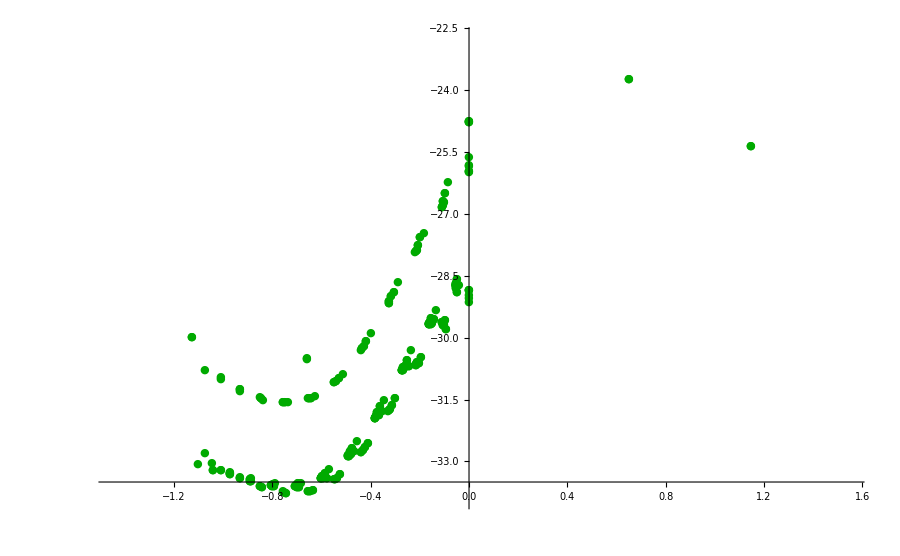

```mathematica
(* vesicle mesh *)
g1=Graphics3D[{Table[Polygon[{points[[polys[[i,1]]]],points[[polys[[i,2]]]],points[[polys[[i,3]]]]}],{i,1,2*NNodes-4}]}, PlotRange->Automatic, ImageSize->IMSize, Boxed-> False, ViewPoint-> Front];Show[g1]

(* plot tension data *)
g2=ListPlot[Table[{points[[i,1]],tensions[[i]][[1]]},{i,1,NNodes}], PlotRange->{{Min[points[[All,1]]]-0.1, Max[points[[All,1]]]+0.1},{Min[tensions]-1,Max[tensions]}+1}, ImageSize->IMSize(*{{1280,1280},{720,720}}*),PlotStyle-> Darker[Green],PlotMarkers->{Automatic,Medium}(*,Epilog-> Inset[g1,{(Min[points[[All,1]]]+Max[points[[All,1]]])/2,Min[tensions]-5}]*)]; Show[g2]

(*(* plot pressure data *)
g3=ListPlot[Table[{facecenters[[i,1]],pressures[[i]][[1]]},{i,1,NFaces}], PlotRange->{{Min[points[[All,1]]]-0.1, Max[points[[All,1]]]+0.1},{Min[pressures],Max[pressures]}}, ImageSize->IMSize(*{{1280,1280},{720,720}}*),PlotStyle-> Darker[Red],PlotMarkers->{Automatic,Medium}(*,Epilog-> Inset[g1,{(Min[points[[All,1]]]+Max[points[[All,1]]])/2,Min[tensions]-5}]*)]; Show[g3]*)
```

```mathematica
(* three-dimensional plots *)
tensmult=.1;(*Artificial scaling factor to magnify the differences in tension into[0,1] range*)
g4=Graphics3D[{Table[Polygon[{points[[polys[[i,1]]]],points[[polys[[i,2]]]],points[[polys[[i,3]]]]},VertexColors->{Hue[tensmult*tensions[[polys[[i,1]]]]],Hue[tensmult*tensions[[polys[[i,2]]]]],Hue[tensmult*tensions[[polys[[i,3]]]]]}],{i,1,2*NNodes-4}]},PlotRange->Automatic,ImageSize->IMSize,Boxed->False,ViewPoint->Front];Show[g4]

(*pressmult=20;(*Artificial scaling factor to magnify the differences in pressure into[0,1] range*)
g5=Graphics3D[{Table[Polygon[{points[[polys[[i,1]]]],points[[polys[[i,2]]]],points[[polys[[i,3]]]]},VertexColors->{Hue[pressmult*pressures[[i]]],Hue[pressmult*pressures[[i]]],Hue[pressmult*pressures[[i]]]}],{i,1,2*NNodes-4}]},PlotRange->Automatic,ImageSize->IMSize,Boxed->False,ViewPoint->Front];Show[g5]*)
```

-Graphics3D-

```mathematica
(* export data to file *)
shapeOutput={points[[All,1]],points[[All,2]],points[[All,3]]};
pressOutput={facecenters[[All,1]],Flatten[pressures]};
tensOutput={points[[All,1]],Flatten[tensions]};
Export["shape.dat",shapeOutput]
Export["pressures.dat",pressOutput]
Export["tensions.dat",tensOutput]
```

shape.dat

pressures.dat

tensions.dat

```mathematica
Mean[tensions]
Mean[pressures]
```

{327.413}

{-0.313358}